```mathematica
ap[t_]:=ap0 Exp[-gamP[Δ] t] Exp[ⅈ OmP[Δ] t];
am[t_]:=am0 Exp[-gamM[Δ] t] Exp[ⅈ OmM[Δ] t];
gamP[Δ_]:=γ0/2+Abs[Λ]/((κm/2)^2+Δm[Δ]^2) κm/2;
gamM[Δ_]:=γ0/2+Abs[Λ]/((κp/2)^2+Δp[Δ]^2) κp/2;
OmP[Δ_]:=Δs+Γ-Abs[Λ]^2/((κm/2)^2+Δm[Δ]^2) Δm[Δ];
OmM[Δ_]:=Δs+Γ-Abs[Λ]^2/((κp/2)^2+Δp[Δ]^2) Δp[Δ];
Δm[Δ_]:=δ0-Δ;
Δp[Δ_]:=δ0+Δ;
```

```mathematica
FullSimplify[ap[t]/am[t]/.{κp->κ,κm->κ,δ0->0},{γ0>=0,Γ∈Reals,κ>=0}]
```

(ap0 ⅇ^((8 ⅈ t Δ Λ Conjugate[Λ])/(4 Δ^2+κ^2)))/am0

```mathematica
α={{1/2(Zpp+Zmm), ⅈ/2(Zpp-Zmm),0},{-ⅈ/2(Zpp-Zmm),1/2(Zpp+Zmm),0},{0,0,Z00}};
U={1/(√2){1,ⅈ,0},{0,0,1},1/(√2){1,-ⅈ,0}};
α//MatrixForm
U.α.ConjugateTranspose[U]//FullSimplify//MatrixForm
```

((Zmm+Zpp)/2 | 1/2 ⅈ (-Zmm+Zpp) | 0
-1/2 ⅈ (-Zmm+Zpp) | (Zmm+Zpp)/2 | 0
0 | 0 | Z00)

(Zpp | 0 | 0
0 | Z00 | 0
0 | 0 | Zmm)

```mathematica
chi3G[i_,j_]:=Sum[(A[m]) (Sum[Ep[m,k]*Ep[m,k]*,{k,1,3}]) KroneckerDelta[i,j] + B[m] Ep[m,i] Ep[m,j]*+C0[m] Ep[m,i]* Ep[m,j],{m,1,2}];
```

```mathematica
Table[chi3G[i,j],{i,1,3},{j,1,3}]//FullSimplify//TraditionalForm//MatrixForm
chi3effOpp=(Table[chi3G[i,j],{i,1,3},{j,1,3}]/.{Ep[1,1]->1/(√2) Ep[1],Ep[1,2]->ⅈ/(√2) Ep[1],Ep[1,3]->0,Ep[2,1]->1/(√2) Ep[2],Ep[2,2]->-ⅈ/(√2) Ep[2],Ep[2,3]->0})//FullSimplify;
chi3effCo=(Table[chi3G[i,j],{i,1,3},{j,1,3}]/.{Ep[1,1]->1/(√2) Ep[1],Ep[1,2]->ⅈ/(√2) Ep[1],Ep[1,3]->0,Ep[2,1]->1/(√2) Ep[2],Ep[2,2]->ⅈ/(√2) Ep[2],Ep[2,3]->0})//FullSimplify;
```

(Abs[Ep(1,1)]^2 (A(1)+B(1)+C0(1))+Abs[Ep(2,1)]^2 (A(2)+B(2)+C0(2))+A(1) (Abs[Ep(1,2)]^2+Abs[Ep(1,3)]^2)+A(2) (Abs[Ep(2,2)]^2+Abs[Ep(2,3)]^2) | B(1) Ep(1,1) Conjugate[Ep(1,2)]+B(2) Ep(2,1) Conjugate[Ep(2,2)]+C0(1) Ep(1,2) Conjugate[Ep(1,1)]+C0(2) Ep(2,2) Conjugate[Ep(2,1)] | B(1) Ep(1,1) Conjugate[Ep(1,3)]+B(2) Ep(2,1) Conjugate[Ep(2,3)]+C0(1) Ep(1,3) Conjugate[Ep(1,1)]+C0(2) Ep(2,3) Conjugate[Ep(2,1)]
B(1) Ep(1,2) Conjugate[Ep(1,1)]+B(2) Ep(2,2) Conjugate[Ep(2,1)]+C0(1) Ep(1,1) Conjugate[Ep(1,2)]+C0(2) Ep(2,1) Conjugate[Ep(2,2)] | Abs[Ep(1,2)]^2 (A(1)+B(1)+C0(1))+Abs[Ep(2,2)]^2 (A(2)+B(2)+C0(2))+A(1) Abs[Ep(1,1)]^2+A(1) Abs[Ep(1,3)]^2+A(2) Abs[Ep(2,1)]^2+A(2) Abs[Ep(2,3)]^2 | B(1) Ep(1,2) Conjugate[Ep(1,3)]+B(2) Ep(2,2) Conjugate[Ep(2,3)]+C0(1) Ep(1,3) Conjugate[Ep(1,2)]+C0(2) Ep(2,3) Conjugate[Ep(2,2)]
B(1) Ep(1,3) Conjugate[Ep(1,1)]+B(2) Ep(2,3) Conjugate[Ep(2,1)]+C0(1) Ep(1,1) Conjugate[Ep(1,3)]+C0(2) Ep(2,1) Conjugate[Ep(2,3)] | B(1) Ep(1,3) Conjugate[Ep(1,2)]+B(2) Ep(2,3) Conjugate[Ep(2,2)]+C0(1) Ep(1,2) Conjugate[Ep(1,3)]+C0(2) Ep(2,2) Conjugate[Ep(2,3)] | Abs[Ep(1,3)]^2 (A(1)+B(1)+C0(1))+Abs[Ep(2,3)]^2 (A(2)+B(2)+C0(2))+A(1) Abs[Ep(1,1)]^2+A(1) Abs[Ep(1,2)]^2+A(2) Abs[Ep(2,1)]^2+A(2) Abs[Ep(2,2)]^2)

```mathematica
chi3effOppCirc = U.chi3effOpp.ConjugateTranspose[U]//FullSimplify;
chi3effCoCirc = U.chi3effCo.ConjugateTranspose[U]//FullSimplify;
```

```mathematica
chi3effOppCirc//MatrixForm
chi3effCoCirc//MatrixForm
chi3effOppCirc[[1,1]]-chi3effOppCirc[[2,2]]//FullSimplify
chi3effCoCirc[[1,1]]-chi3effCoCirc[[2,2]]//FullSimplify
```

(Abs[Ep[2]]^2 (A[2]+B[2])+Abs[Ep[1]]^2 (A[1]+C0[1]) | 0 | 0
0 | Abs[Ep[1]]^2 (A[1]+B[1])+Abs[Ep[2]]^2 (A[2]+C0[2]) | 0
0 | 0 | A[1] Abs[Ep[1]]^2+A[2] Abs[Ep[2]]^2)

(Abs[Ep[1]]^2 (A[1]+C0[1])+Abs[Ep[2]]^2 (A[2]+C0[2]) | 0 | 0
0 | Abs[Ep[1]]^2 (A[1]+B[1])+Abs[Ep[2]]^2 (A[2]+B[2]) | 0
0 | 0 | A[1] Abs[Ep[1]]^2+A[2] Abs[Ep[2]]^2)

Abs[Ep[1]]^2 (-B[1]+C0[1])+Abs[Ep[2]]^2 (B[2]-C0[2])

Abs[Ep[1]]^2 (-B[1]+C0[1])+Abs[Ep[2]]^2 (-B[2]+C0[2])

```mathematica
chi3effOpp//MatrixForm
```

(1/2 (Abs[Ep[1]]^2 (2 A[1]+B[1]+C0[1])+Abs[Ep[2]]^2 (2 A[2]+B[2]+C0[2])) | -1/2 ⅈ (Abs[Ep[1]]^2 (B[1]-C0[1])+Abs[Ep[2]]^2 (-B[2]+C0[2])) | 0
1/2 ⅈ (Abs[Ep[1]]^2 (B[1]-C0[1])+Abs[Ep[2]]^2 (-B[2]+C0[2])) | 1/2 (Abs[Ep[1]]^2 (2 A[1]+B[1]+C0[1])+Abs[Ep[2]]^2 (2 A[2]+B[2]+C0[2])) | 0
0 | 0 | A[1] Abs[Ep[1]]^2+A[2] Abs[Ep[2]]^2)

```mathematica
chi3Boyd[E_List,i_,j_]:=(A-1/2 B) Sum[(E[[k]]) (E[[k]])*,{k,1,3}] KroneckerDelta[i,j] + B/2 ((E[[i]]) (E[[j]])* +(E[[i]])* (E[[j]]));
```

```mathematica
chi3EffBoyd=Table[chi3Boyd[Ep/(√2) {1,ⅈ,0}+Em/(√2) {1,-ⅈ,0},i,j],{i,1,3},{j,1,3}]//FullSimplify;
```

```mathematica
U.chi3EffBoyd.ConjugateTranspose[U]//FullSimplify//MatrixForm
```

(A (Abs[Em]^2+Abs[Ep]^2) | 0 | B Em Conjugate[Ep]
0 | 1/2 (2 A-B) (Abs[Em]^2+Abs[Ep]^2) | 0
B Ep Conjugate[Em] | 0 | A (Abs[Em]^2+Abs[Ep]^2))

```mathematica
U.(Ep/(√2) {1,ⅈ,0}+Em/(√2) {1,-ⅈ,0})//FullSimplify
```

{Em,0,Ep}

```mathematica
U.(chi3EffBoyd.(Ep/(√2) {1,ⅈ,0}+Em/(√2) {1,-ⅈ,0}))//FullSimplify
```

{Em (A Em Conjugate[Em]+(A+B) Ep Conjugate[Ep]),Ep ((A+B) Em Conjugate[Em]+A Ep Conjugate[Ep]),0}

```mathematica
pBoyd[E_List]:=A*(E.E*) E + 1/2 B (E.E)*E*;
U.pBoyd[Ep/(√2) {1, ⅈ, 0}+Em/(√2) {1, -ⅈ, 0}]//FullSimplify
```

{Em (A Em Conjugate[Em]+(A+B) Ep Conjugate[Ep]),Ep ((A+B) Em Conjugate[Em]+A Ep Conjugate[Ep]),0}

```mathematica
U.DiagonalMatrix[{a,b,c}].ConjugateTranspose[U]//MatrixForm
U.DiagonalMatrix[{a,b,c}].ConjugateTranspose[U].{p1,0,0}//MatrixForm
```

(a/2+b/2 | 0 | a/2-b/2
0 | c | 0
a/2-b/2 | 0 | a/2+b/2)

((a/2+b/2) p1
0
(a/2-b/2) p1)

```mathematica
U
```

{{1/(√2),ⅈ/(√2),0},{0,0,1},{1/(√2),-ⅈ/(√2),0}}

```mathematica
U[[3,All]].DiagonalMatrix[{a,b,c}].Conjugate[U[[3,All]]]
```

a/2+b/2

```mathematica
Manipulate[Plot[1/(Exp[-t/τ]+1)-HeavisideTheta[t],{t,-10,10},PlotRange->All],{τ,0.1,1}]
```

```mathematica
n[t_]:=ni+Δn/2 (1+Tanh[t/τ]);
ω[t_]:=c k / n[t];
```

```mathematica
D[ω[t],t]/ω[t]//FullSimplify
```

-(Δn Sech[t/τ]^2)/(2 ni τ+Δn τ+Δn τ Tanh[t/τ])

```mathematica
Manipulate[Plot[-(Δn Sech[t/τ]^2)/(2 ni τ+Δn τ+Δn τ Tanh[t/τ]),{t,-8,8}],{ni,-8,8},{Δn,-2,2},{τ,-2,2}]
```

```mathematica
FourierTransform[Sech[t/τ]^2,t,Ω]
```

√(π/2) τ^2 Ω Csch[(π τ Ω)/2]

```mathematica
Series[η Csch[(π η)/2],{η,0,3}]
```

2/π-(π η^2)/12+O[η]^4

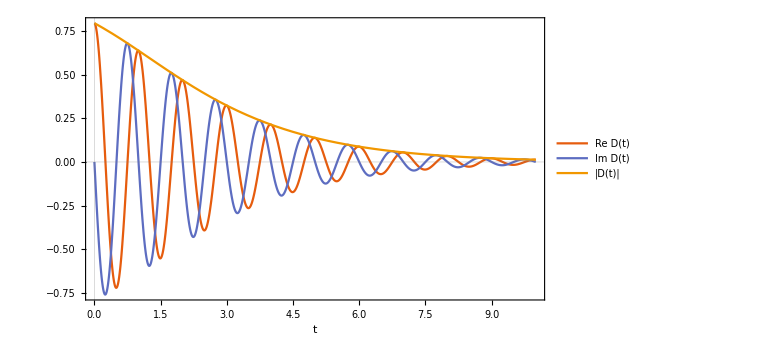

```mathematica
(*Clear and define*)ClearAll["Global`*"];

Dfun[t_,a_,b_,c_,τ0_,ωj_,D0_:1]:=Module[{z,term1,term2},z=-Exp[-t/τ0];
term1=Gamma[c] Gamma[b-a]/(Gamma[b] Gamma[c-a])*Exp[-a t/τ0]*Hypergeometric2F1[a,a+1-c,a+1-b,z];
term2=Gamma[c] Gamma[a-b]/(Gamma[a] Gamma[c-b])*Exp[-b t/τ0]*Hypergeometric2F1[b,b+1-c,b+1-a,z];
D0*Exp[-I ωj t]*(term1+term2)];

(*---Example parameters (avoid poles of Gamma)---*)
pars=<|"a"->1/2,"b"->3/4,"c"->7/6,"τ0"->1.0,"ωj"->2 Pi,"D0"->1|>;

(*Plot Re,Im,and|D|over t>0*)
Plot[Evaluate@{Re@Dfun[t,pars["a"],pars["b"],pars["c"],pars["τ0"],pars["ωj"],pars["D0"]],Im@Dfun[t,pars["a"],pars["b"],pars["c"],pars["τ0"],pars["ωj"],pars["D0"]],Abs@Dfun[t,pars["a"],pars["b"],pars["c"],pars["τ0"],pars["ωj"],pars["D0"]]},{t,0,10},PlotLegends->{"Re D(t)","Im D(t)","|D(t)|"},AxesLabel->{"t",None},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
```

{{ap→InterpolatingFunction[…],am→InterpolatingFunction[…]}}

{{ap→InterpolatingFunction[…],am→InterpolatingFunction[…]}}

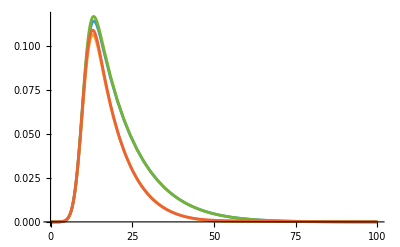

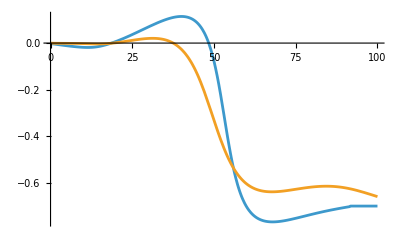

```mathematica
S[t_,a0_,t0_,τ_]:=a0 Exp[-(t-t0)^2/τ^2];
tmax=100;
sol = NDSolve[{ap'[t]==ⅈ d Exp[ⅈ Δ t] (2 ⅈ (ω+Δ) am'[t]-(ω+Δ)^2 am[t] ) -γ ap[t] + √γ S[t,0.1,10,3],
am'[t]==ⅈ d* Exp[-ⅈ Δ t] (2 ⅈ (ω-Δ) ap'[t]-(ω-Δ)^2 ap[t] ) -γ am[t] + √γ S[t,0.1,10,3],am[0]==0,ap[0]==0}/.{Δ->0.05,ω->1,γ->0.1,d->0.02+ⅈ 0.001},{ap,am},{t,0,tmax}]
sol0 = NDSolve[{ap'[t]==ⅈ d Exp[ⅈ Δ t] (-(ω+Δ)^2 am[t] ) -γ ap[t] + √γ S[t,0.1,10,3],
am'[t]==ⅈ d* Exp[-ⅈ Δ t] (-(ω-Δ)^2 ap[t] ) -γ am[t] + √γ S[t,0.1,10,3],am[0]==0,ap[0]==0}/.{Δ->0.05,ω->1,γ->0.1,d->0.02+ⅈ 0.001},{ap,am},{t,0,tmax}]

Plot[Evaluate@Abs@{ap[t]/.sol[[1]],am[t]/.sol[[1]],ap[t]/.sol0[[1]],am[t]/.sol0[[1]]},{t,0,tmax},PlotRange->All]
Plot[Evaluate@{0.5*Arg[ap[t]/am[t]]/.sol[[1]],0.5*Arg[ap[t]/am[t]]/.sol0[[1]]},{t,0,tmax},PlotRange->All]
```

```mathematica
sol1 = DSolve[{ap'[t]==(ⅈ δ-κ)/2 ap[t] +ⅈ Λ Abs[A1]^2 Abs[A2]^2 gm/(-Δ + ⅈ κ/2) ap[t]+√κ a0 Exp[(-(t-t0)^2)/τ^2],ap[0]==0,
am'[t]==(ⅈ δ-κ)/2 am[t] +ⅈ Λ Abs[A1]^2 Abs[A2]^2 gm/(Δ + ⅈ κ/2) am[t]+√κ a0 Exp[(-(t-t0)^2)/τ^2],am[0]==0},{ap,am},t]//FullSimplify
sol2 = DSolve[{ap'[t]==(ⅈ δ-κ)/2 ap[t] +ⅈ Λ Abs[A1]^2 Abs[A2]^2 gm/(-Δ + ⅈ κ/2) ap[t]+√κ a0,ap[0]==0,
am'[t]==(ⅈ δ-κ)/2 am[t] +ⅈ Λ Abs[A1]^2 Abs[A2]^2 gm/(Δ + ⅈ κ/2) am[t]+√κ a0,am[0]==0},{ap,am},t]//FullSimplify
```

{{ap→Function[{t},-1/2 ⅈ a0 ⅇ^((t ((δ+ⅈ κ) (2 ⅈ Δ+κ)-4 ⅈ gm Λ Abs[A1]^2 Abs[A2]^2))/(4 Δ-2 ⅈ κ)-(((-ⅈ δ+κ) (2 ⅈ Δ+κ)-4 gm Λ Abs[A1]^2 Abs[A2]^2) ((2 ⅈ Δ+κ) (8 t0+(-ⅈ δ+κ) τ^2)-4 gm Λ τ^2 Abs[A1]^2 Abs[A2]^2))/(16 (2 Δ-ⅈ κ)^2)) √π √κ τ (Erfi[((2 ⅈ Δ+κ) (4 t0+(-ⅈ δ+κ) τ^2)-4 gm Λ τ^2 Abs[A1]^2 Abs[A2]^2)/(8 Δ τ-4 ⅈ κ τ)]-Erfi[((2 ⅈ Δ+κ) (-4 t+4 t0+(-ⅈ δ+κ) τ^2)-4 gm Λ τ^2 Abs[A1]^2 Abs[A2]^2)/(8 Δ τ-4 ⅈ κ τ)])],am→Function[{t},-1/2 ⅈ a0 ⅇ^((ⅈ t ((δ+ⅈ κ) (2 Δ+ⅈ κ)+4 gm Λ Abs[A1]^2 Abs[A2]^2))/(4 Δ+2 ⅈ κ)-(((δ+ⅈ κ) (2 Δ+ⅈ κ)+4 gm Λ Abs[A1]^2 Abs[A2]^2) ((2 Δ+ⅈ κ) (8 ⅈ t0+(δ+ⅈ κ) τ^2)+4 gm Λ τ^2 Abs[A1]^2 Abs[A2]^2))/(16 (2 Δ+ⅈ κ)^2)) √π √κ τ (Erfi[((2 Δ+ⅈ κ) (4 ⅈ t0+(δ+ⅈ κ) τ^2)+4 gm Λ τ^2 Abs[A1]^2 Abs[A2]^2)/(8 Δ τ+4 ⅈ κ τ)]-Erfi[((2 Δ+ⅈ κ) (-4 ⅈ t+4 ⅈ t0+(δ+ⅈ κ) τ^2)+4 gm Λ τ^2 Abs[A1]^2 Abs[A2]^2)/(8 Δ τ+4 ⅈ κ τ)])]}}

{{ap→Function[{t},-((2 a0 ⅇ^((ⅈ t δ Δ)/(2 Δ-ⅈ κ)+(t δ κ)/(2 (2 Δ-ⅈ κ))-(t Δ κ)/(2 Δ-ⅈ κ)+(ⅈ t κ^2)/(2 (2 Δ-ⅈ κ))-(2 ⅈ gm t Λ Abs[A1]^2 Abs[A2]^2)/(2 Δ-ⅈ κ)-(t ((δ+ⅈ κ) (2 ⅈ Δ+κ)-4 ⅈ gm Λ Abs[A1]^2 Abs[A2]^2))/(4 Δ-2 ⅈ κ)) (-1+ⅇ^((t ((δ+ⅈ κ) (2 ⅈ Δ+κ)-4 ⅈ gm Λ Abs[A1]^2 Abs[A2]^2))/(4 Δ-2 ⅈ κ))) (2 Δ-ⅈ κ) √κ)/(-2 ⅈ δ Δ-δ κ+2 Δ κ-ⅈ κ^2+4 ⅈ gm Λ Abs[A1]^2 Abs[A2]^2))],am→Function[{t},(2 a0 ⅇ^((ⅈ t δ Δ)/(2 Δ+ⅈ κ)-(t δ κ)/(2 (2 Δ+ⅈ κ))-(t Δ κ)/(2 Δ+ⅈ κ)-(ⅈ t κ^2)/(2 (2 Δ+ⅈ κ))+(2 ⅈ gm t Λ Abs[A1]^2 Abs[A2]^2)/(2 Δ+ⅈ κ)-(ⅈ t ((δ+ⅈ κ) (2 Δ+ⅈ κ)+4 gm Λ Abs[A1]^2 Abs[A2]^2))/(4 Δ+2 ⅈ κ)) (-1+ⅇ^((ⅈ t ((δ+ⅈ κ) (2 Δ+ⅈ κ)+4 gm Λ Abs[A1]^2 Abs[A2]^2))/(4 Δ+2 ⅈ κ))) (2 Δ+ⅈ κ) √κ)/(2 ⅈ δ Δ-δ κ-2 Δ κ-ⅈ κ^2+4 ⅈ gm Λ Abs[A1]^2 Abs[A2]^2)]}}

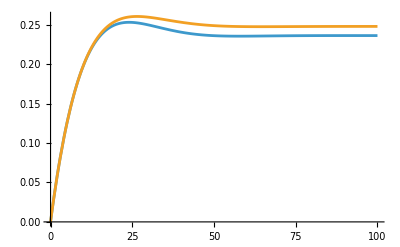

```mathematica
Plot[Evaluate@Abs@({(ap[t]/.sol2[[1]]),(am[t]/.sol2[[1]])}/.{Δ->0.1,δ->0.01,κ->0.1,Λ->10.5+ⅈ 0.01,gm->-10.7+ⅈ 0.1,a0->0.1,t0->10,τ->5,A1->0.1,A2->0.1}),{t,0,tmax},PlotRange->All]
```

```mathematica
Manipulate[{DensityPlot[
Abs@(√κ  ap[t]/.sol2[[1]])/.{Δ->0.1,δ->del,κ->0.1,Λ->10.2+ⅈ 0.01,gm->-10.7+ⅈ 0.1,a0->0.1,t0->10,τ->10,A1->ii,A2->ii}(*/.{Δ->0.05,ω->1+del,γ->0.1,d->ii+ⅈ 0.001,a0->0.1,t0->10,τ->3}*),{del,-1,1},{ii,0,0.2},PlotRange->All,PlotLegends->Automatic
],DensityPlot[
Abs@(√κ  am[t]/.sol2[[1]])/.{Δ->0.1,δ->del,κ->0.1,Λ->10.2+ⅈ 0.01,gm->-10.7+ⅈ 0.1,a0->0.1,t0->10,τ->10,A1->ii,A2->ii}(*/.{Δ->0.05,ω->1+del,γ->0.1,d->ii+ⅈ 0.001,a0->0.1,t0->10,τ->3}*),{del,-1,1},{ii,0,0.2},PlotRange->All,PlotLegends->Automatic
],
DensityPlot[
Abs@(√κ  (ap[t]+ⅈ am[t])/.sol2[[1]])/.{Δ->0.1,δ->del,κ->0.1,Λ->30.2+ⅈ 0.01,gm->-30.7+ⅈ 0.1,a0->0.1,t0->10,τ->10,A1->ii,A2->ii}(*/.{Δ->0.05,ω->1+del,γ->0.1,d->ii+ⅈ 0.001,a0->0.1,t0->10,τ->3}*),{del,-1,1},{ii,0,0.2},PlotRange->All,PlotLegends->Automatic
]},{t,5,tmax}]
```

```mathematica
sol3 = DSolve[{ap'[t]==(ⅈ δ-κ)/2 ap[t] +ⅈ Λ Abs[A1]^2 Abs[A2]^2 gm/(-Δ + ⅈ κ/2) ap[t],ap[0]==a0,
am'[t]==(ⅈ δ-κ)/2 am[t] +ⅈ Λ Abs[A1]^2 Abs[A2]^2 gm/(Δ + ⅈ κ/2) am[t],am[0]==a0},{ap,am},t]//FullSimplify
```

{{ap→Function[{t},a0 ⅇ^((ⅈ t δ Δ)/(2 Δ-ⅈ κ)+(t δ κ)/(2 (2 Δ-ⅈ κ))-(t Δ κ)/(2 Δ-ⅈ κ)+(ⅈ t κ^2)/(2 (2 Δ-ⅈ κ))-(2 ⅈ gm t Λ Abs[A1]^2 Abs[A2]^2)/(2 Δ-ⅈ κ))],am→Function[{t},a0 ⅇ^((ⅈ t δ Δ)/(2 Δ+ⅈ κ)-(t δ κ)/(2 (2 Δ+ⅈ κ))-(t Δ κ)/(2 Δ+ⅈ κ)-(ⅈ t κ^2)/(2 (2 Δ+ⅈ κ))+(2 ⅈ gm t Λ Abs[A1]^2 Abs[A2]^2)/(2 Δ+ⅈ κ))]}}

```mathematica
1/2 Arg[(ap[t]/am[t])]/.sol3[[1]]//FullSimplify
```

1/2 Arg[ⅇ^(-(8 ⅈ A1 A2 gm t Δ Λ Conjugate[A1] Conjugate[A2])/(4 Δ^2+κ^2))]

```mathematica
ComplexExpand[1/2 Arg[ⅇ^(-(8 ⅈ gm t Δ Λ I1 I2)/(4 Δ^2+κ^2))],TargetFunctions->{Abs, Arg}]//FullSimplify
```

-1/2 ⅈ Log[ⅇ^(-(8 ⅈ gm I1 I2 t Δ Λ)/(4 Δ^2+κ^2))]

```mathematica
Arg[Exp[ⅈ π/2]]
```

π/2

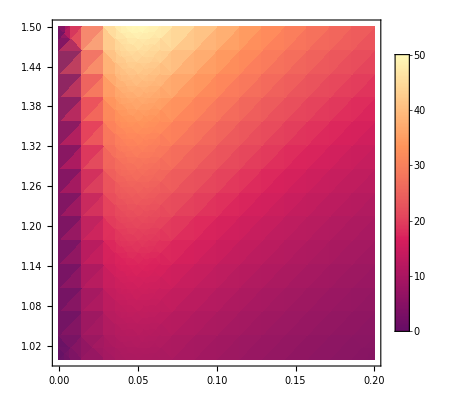

```mathematica
DensityPlot[(4 A^4 Δ)/(4 Δ^2+κ^2)/.{κ->0.1},{Δ,0,0.2},{A,1,1.5},PlotRange->All,PlotLegends->Automatic(*,ScalingFunctions->{None, "Log"}*)]
```

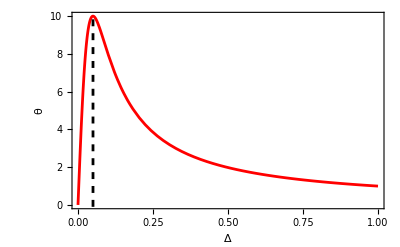

```mathematica
Show[Plot[(4 A^4 Δ)/(4 Δ^2+κ^2)/.{κ->0.1,A->1},{Δ,0,1},PlotStyle->Red,Frame->True,FrameLabel->{"Δ","θ"},BaseStyle->14,FrameTicks->{Automatic,None}],ListPlot[{{0.1/2,-0.1},{0.1/2,10.05}},Joined->True,PlotStyle->{Black,Dashed}]]
```

```mathematica
Solve[{eP == (ex+ⅈ ey)/(√2),eM == (ex-ⅈ ey)/(√2)},{ex,ey}]//Simplify
```

{{ex→(eM+eP)/(√2),ey→(ⅈ (eM-eP))/(√2)}}